```mathematica
(* Find the volume and circumference of a circle *)
myRadius = 5;
myHeight = 5;
theCircleVolume = N[Pi  myRadius^2]
```

78.5398

```mathematica
theCircleCircumference = N[2 Pi myRadius]
```

31.4159

```mathematica
theCylinderVolume =  N[Pi  myRadius^2 myHeight]
```

392.699

```mathematica
(* The cone volume is a third of the cylinder volume *)
theConeVolume = N[1/3  Pi   myRadius^2  myHeight]
```

130.9

```mathematica
(* Find the sphere volume and surface area *)
theSphereVolume = N[4/3  Pi   (myRadius^3)]
```

523.599

```mathematica
theSphereSurfaceArea = N[4  Pi myRadius^2]
```

314.159

```mathematica
(* Find trapezoid area *)
myTrapezoidHeight = 5;
myTrapezoidBottomLength = 10;
myTrapezoidTopLength = 6;
myTrapezoidMidPoint = 1/2  (myTrapezoidBottomLength + myTrapezoidTopLength);
(* Two ways to find trapezoid(US)/trapezium(UK) area: *)
theTrapezoidArea1 = 1/2  myTrapezoidHeight  (myTrapezoidBottomLength + myTrapezoidTopLength)
theTrapezoidArea2 = myTrapezoidMidPoint  myTrapezoidHeight
```

40

40

```mathematica
(* Equation. 6x in answer has to be positive to be in standard form
3x – 4y – 1 = 9x + 5y – 12
	(3-9)x - 4y - 1 = 5y - 12 (move +9x left to -9x)
	-6x - 4y - 1 = 5y - 12 
	-6x - 4y = 5y - 11 (move -1 right to +1)
	-6x - 9y = -11 (move +5y left to -5y)
	Answer: 6x + 9y = 11 (multiply everything with -1)
*)
```

```mathematica
(* Find the line equation of a line. Slope = m *)
(* (yPoint2 – yPoint1) = theSlope * (xPoint2 – xPoint1) *)
(*
y - (-2) = (2/3) * (x - 0)
3y - (-6) = 2x (* Multiply with 3 to get rid of the fraction *)
3y + 6 = 2x
3y = 2x - 6
3y - 2x = -6
2x - 3y = 6
*)
```

```mathematica
(* Simplify tricky exponentials... *)
{N[4^(3/2)], N[(4^(1/2))^3]}
```

{8.,8.}

```mathematica
{N[4^(2/4)], N[(4^(1/4))^2]}
```

{2.,2.}

```mathematica
{N[1/3^(2/3)], N[3^(-2/3)]}
```

{0.48075,0.48075}

```mathematica
(* Some radical expression refreshing... *)
Clear x; Clear y;
x = 3; y = 2;
{N[(1000 x^3 27 y^7)^(1/3)], N[((10*10*10)x^3*(3^3)(y^3*y^3)*y)^(1/3)],N[10x*3 y^2 y^(1/3)]} (* Pull out x^3 and y^3 and 10 cube *)
```

{453.572,453.572,453.572}

```mathematica
{N[(1000 x^3 54 y^7)^(1/3)], N[((10*10*10)x^3*(3^3)*2*(y^3*y^3)*y)^(1/3)],N[10x*3 y^2(2y)^(1/3)]}
```

{571.464,571.464,571.464}

```mathematica
x = 3; y = 2;
{N[(1000 x^3 12 y^7)^(1/2)], N[(((10*10*10)x^2*x)*(2^2*3(y^2*y^2*y^2)*y))^(1/2)],N[10x*2 y^3(10x*3y)^(1/2)]}
```

{6439.88,6439.88,6439.88}

```mathematica
{N[√(x^3 49 x^2)], N[√((x * x^2)*(7^2*x^2))],N[7 x^2 √x]}
```

{109.119,109.119,109.119}

```mathematica
{N[√(2 x^2*3x)], N[√(2(x * x)*(3x))],N[Abs[x] √(6x)]}
```

{12.7279,12.7279,12.7279}

```mathematica
x = -3; y = -2;
{N[√(2 x^2*3x)], N[√(2(x * x)*(3x))],N[Abs[x] √(6x)]} (* Note: Negative values. Use ABS to ensure positive result *)
```

{0.+12.7279 ⅈ,0.+12.7279 ⅈ,0.+12.7279 ⅈ}

Creating matrices for Sisalike stairs carpet and metal lists for stairs edges...

```mathematica
sisalikeMatrix:=({{0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 2, 2, 2, 2, 2, 2, 2, 2, 3, 3, 3, 3, 3, 3, 3, 3, 4, 4, 4, 4, 4, 4, 4, 4, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 2, 2, 2, 2, 2, 2, 2, 2, 3, 3, 3, 3, 3, 3, 3, 3, 4, 4, 4, 4, 4, 4, 4, 4, 0, 0, 0, 0, 0, 0, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 2, 2, 2, 2, 2, 2, 2, 2, 3, 3, 3, 3, 3, 3, 3, 3, 4, 4, 4, 4, 4, 4, 4, 4, 0, 0, 0, 0, 0, 0, 0, 0}, {5, 5, 5, 5, 5, 5, 5, 5, 6, 6, 6, 6, 6, 6, 6, 6, 7, 7, 7, 7, 7, 7, 7, 7, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 0, 0, 0, 0}, {5, 5, 5, 5, 5, 5, 5, 5, 6, 6, 6, 6, 6, 6, 6, 6, 7, 7, 7, 7, 7, 7, 7, 7, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 0, 0, 0, 0}, {5, 5, 5, 5, 5, 5, 5, 5, 6, 6, 6, 6, 6, 6, 6, 6, 7, 7, 7, 7, 7, 7, 7, 7, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 0, 0, 0, 0}, {13, 13, 13, 13, 13, 13, 13, 13, 13, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 0, 0, 0, 0}, {13, 13, 13, 13, 13, 13, 13, 13, 13, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 0, 0, 0, 0}, {9, 9, 9, 9, 9, 9, 9, 9, 9, 9, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 12, 12, 12, 12, 12, 12, 12, 12, 12, 8, 8, 8, 8, 8, 8, 8, 8, 0, 0}, {9, 9, 9, 9, 9, 9, 9, 9, 9, 9, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 12, 12, 12, 12, 12, 12, 12, 12, 12, 8, 8, 8, 8, 8, 8, 8, 8, 0, 0}, {9, 9, 9, 9, 9, 9, 9, 9, 9, 9, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 12, 12, 12, 12, 12, 12, 12, 12, 12, 8, 8, 8, 8, 8, 8, 8, 8, 0, 0}, {9, 9, 9, 9, 9, 9, 9, 9, 9, 9, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 12, 12, 12, 12, 12, 12, 12, 12, 12, 8, 8, 8, 8, 8, 8, 8, 8, 0, 0}, {9, 9, 9, 9, 9, 9, 9, 9, 9, 9, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 12, 12, 12, 12, 12, 12, 12, 12, 12, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}});
TableView[sisalikeMatrix]
```

1:eJxTTMoPSmJiYGDgB2INBuIBIxQwQQEzFLBAAa3UsUIBGxSwQwEXEqCFOl4Y
QAsHctVxwgE3AvDAAAcUDFZ1JCQUKAAAD0wO/Q==

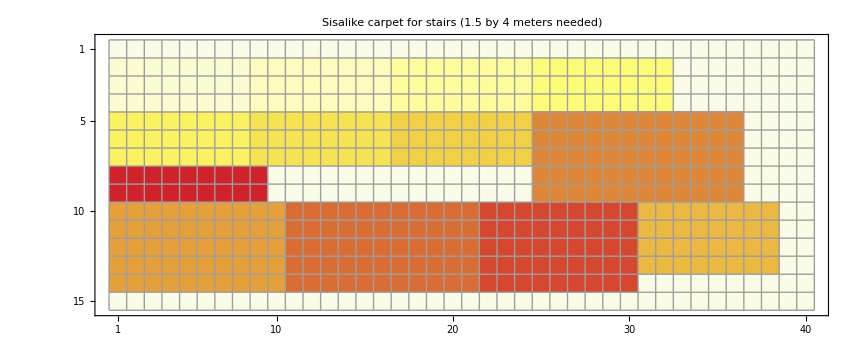

```mathematica
dimensions:=Row[{"Sisalike carpet for stairs (", N[Dimensions[sisalikeMatrix] / 10][[1]]," by ",
 Dimensions[sisalikeMatrix][[2]] / 10, " meters needed)"}]
MatrixPlot[sisalikeMatrix, ColorFunction->"TemperatureMap", (* GridLines->{Range[40], Automatic}, *) Mesh->True,
PlotLabel->dimensions]
```

```mathematica
stepListMatrix:=({{1, 1, 1, 1, 1, 1, 1, 1, 2, 2, 2, 2, 2, 2, 2, 2, 3, 3, 3, 3, 3, 3, 3, 3, 0, 0, 0}, {4, 4, 4, 4, 4, 4, 4, 4, 5, 5, 5, 5, 5, 5, 5, 5, 6, 6, 6, 6, 6, 6, 6, 6, 0, 0, 0}, {7, 7, 7, 7, 7, 7, 7, 7, 8, 8, 8, 8, 8, 8, 8, 8, 9, 9, 9, 9, 9, 9, 9, 9, 9, 9, 0}, {10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 10, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 11, 0, 0, 0, 0}, {12, 12, 12, 12, 12, 12, 12, 12, 12, 12, 13, 13, 13, 13, 13, 13, 13, 13, 13, 0, 0, 0, 0, 0, 0, 0, 0}})
```

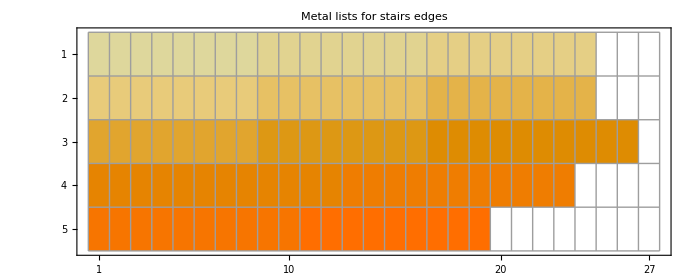

```mathematica
MatrixPlot[stepListMatrix, Mesh->True, PlotLabel->"Metal lists for stairs edges"]
```

```mathematica
(* Inversions and permutations - to be used on 15Puzzle code to determine whether a randomiz<tion is solvable or not *)
(* http://mathworld.wolfram.com/PermutationInversion.html *)
A = RandomInteger[15, 16];
A = Flatten[RandomPermutation[16]];
A = RandomSample[Range[16], 16]
B = Permutations[A[[Range[4]]]]
ToInversionVector[A[[Range[4]]]]
Factorial[4]
Factorial[16] (* 20922789888000 possible combinations! *)
```

{8,15,13,9,2,3,5,12,16,6,11,14,4,10,1,7}

{{8,15,13,9},{8,15,9,13},{8,13,15,9},{8,13,9,15},{8,9,15,13},{8,9,13,15},{15,8,13,9},{15,8,9,13},{15,13,8,9},{15,13,9,8},{15,9,8,13},{15,9,13,8},{13,8,15,9},{13,8,9,15},{13,15,8,9},{13,15,9,8},{13,9,8,15},{13,9,15,8},{9,8,15,13},{9,8,13,15},{9,15,8,13},{9,15,13,8},{9,13,8,15},{9,13,15,8}}

ToInversionVector[{8,15,13,9}]

24

20922789888000